```mathematica
N[Solve[1-x1-x2/(1+x2) -x3/(1+x3) - x4/(1+x4)==0&&1-x2-x1/(1+x1) - x3/(1+x3)- x4/(1+x4)==0&&1-x3-x1/(1+x1) - x2/(1+x2)- x4/(1+x4)==0&&1-x3/(1+x3)-x1/(1+x1) - x2/(1+x2) - x4== 0, {x1, x2, x3, x4}]]
```

{{x1→-0.5,x2→1.,x3→1.,x4→1.},{x1→1.,x2→1.,x3→-0.5,x4→1.},{x1→1.,x2→1.,x3→1.,x4→-0.5},{x1→1.,x2→-0.5,x3→1.,x4→1.},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-2.59808 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.0540541+0.324324 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.945946-0.324324 ⅈ},{x1→-3.30278,x2→-3.30278,x3→-3.30278,x4→-3.30278},{x1→0.302776,x2→0.302776,x3→0.302776,x4→0.302776}}

```mathematica
ContourPlot[{2+5*x1-x2/(1+x2)==0,2+5*x2-x1/(1+x1)==0 }, {x1, -5, 5}, {x2, -5, 5}];
```

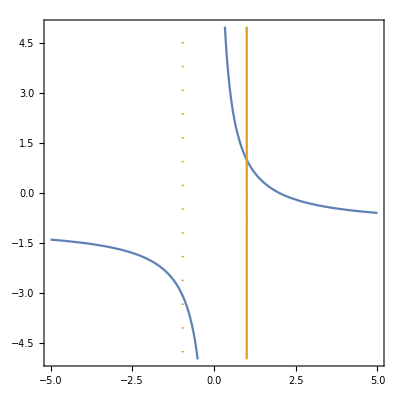

```mathematica
ContourPlot[{1-a11*x1+2*(a11-1)*x2/(1+x2)==0,1-(1-2*a11)*x2-4*a11*x1/(1+x1)==0}, {x1, -5, 5}, {x2, -5, 5}]
```

```mathematica
a11 = a11;
N[Solve[1-a11*x1+2*(a11-1)*x2/(1+x2)==0&&1-(1-2*a11)*x2-4*a11*x1/(1+x1)==0 {x1, x2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→1.,x2→1.}}

```mathematica
FullSimplify[Solve[1-a11*x1+a12*x2/(1+x2)==0, {x2}][[1]][[1]][[2]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(-2.+x1)/(2.+2. a12-1. x1)
```

(-2.+x1)/(2.+2. a12-1. x1)

# Imposing tangency on a feasible planted equilibrium

```mathematica
Clear[a11];
eq1 = 1 - a11*x1 + a12*x2/(1 + x2) + a13*x3/(1+x3);
eq2 = 1 - a22*x2 - a21*x1/(1 + x1)+ a23*x3/(1+x3);eq3 = 1 - a33*x3 - a31*x1/(1 + x1)+ a32*x2/(1+x2);
```

```mathematica
constr1 = eq1/.x1-> 1/.x2->1 /.x3->1 ;
constr2 = eq2/.x1-> 1/.x2->1/.x3->1 ;
constr3 = eq3/.x1-> 1/.x2->1/.x3->1;
```

```mathematica
curve1 = Solve[eq1==0, x3][[1]][[1]][[2]];
curve2 = Solve[eq2==0, x3][[1]][[1]][[2]];
curve2 = Solve[eq2==0, x3][[1]][[1]][[2]];
```

(1+x1-a21 x1-a22 x2-a22 x1 x2)/(-1-a23-x1+a21 x1-a23 x1+a22 x2+a22 x1 x2)

```mathematica
derivative1 = D[curve1, x1]/.x1->1/.x2->1/.x3->1;
```

```mathematica
derivative2 = D[curve2, x1]/.x1->1/.x2->1/.x3->1;
```

```mathematica
Solve[constr1 == 0 && constr2 ==0&& derivative1==derivative2, {a12, a21, a22}]
```

{{a12→2 (-1+a11),a21→(8 a11)/(1+3 a11),a22→(1-a11)/(1+3 a11)}}

```mathematica
eq1constr = eq1/.a12->2 (-1+a11) +RandomReal[{-0.1, 0.1}]/.a21->(8 a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}]/.a22->(1-a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}];
eq2constr = eq2/.a12->2 (-1+a11)+RandomReal[{-0.1, 0.1}]/.a21->(8 a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}]/.a22->(1-a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}];
```

```mathematica
a11 = 0.5;
Solve[eq1constr==0&&eq2constr==0, {x1, x2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.822035,x2→1.44715},{x1→1.99238,x2→0.00383864}}

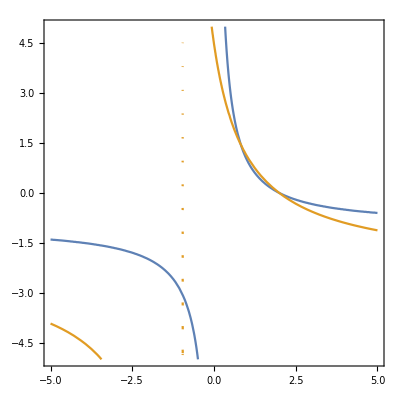

```mathematica
ContourPlot[{eq1constr, eq2constr}, {x1, -5, 5}, {x2, -5, 5}]
```

```mathematica
FullSimplify[n+1/2*n*(n-1)]
```

1/2 n (1+n)

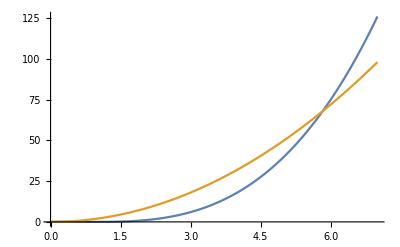

```mathematica
1/2 n (1+n)
Plot[{Binomial[n, 2]*(n-1), 2*n^2}, {n, 0, 7}]
```

## Putting glv with functional responses in polynomial form

```mathematica
Clear[a11]
eq1 = (1+x2)*(1+x3)*(r1 - a11*x1)+ x2*a12*(1+x3) + x3*a13*(1+x2);
MonomialList[eq1, {x1, x2, x3}]
```

{-a11 x1 x2 x3,-a11 x1 x2,-a11 x1 x3,-a11 x1,(a12+a13+r1) x2 x3,(a12+r1) x2,(a13+r1) x3,r1}

### Bidirectional mutualism in C-R

```mathematica
eq1 =(h2+x2)*(h3+x3)*(e1+x1)*(r1 - a11*x1) + a12*x2*(h3+x3)*(e1+x1) + a13*x3*(h2+x2)*(e1+x1)-(b31*x3 + b21*x2)*(h2+x2)*(h3+x3);
eq2 = (h1+x1)*(h3+x3)*(e2+x2)*(r2-a22*x2) + a21*x1*(h3+x3)*(e2+x2) + a23*x3*(h1+x1)*(e2+x2) - (b12*x1 + b32*x3)*(h1+x1)*(h3+x3);
eq3 = (h1+x1)*(h2+x2)*(e3+x3)*(r3-a33*x3) + a31*x1*(e3 + x3)*(h2+x2)+  a32*x2*(h1+x1)*(e3+x3)-(b13*x1+b32*x2)*(h1 + x1)*(h2+x2);
```

```mathematica
MonomialList[{eq1, eq2, eq3}, {x1, x2, x3}, "DegreeLexicographic"]
```

{{-a11 x1^2 x2 x3,-a11 h3 x1^2 x2,-a11 h2 x1^2 x3,(a12+a13-a11 e1+r1) x1 x2 x3,-b21 x2^2 x3,-b31 x2 x3^2,-a11 h2 h3 x1^2,(a12 h3-a11 e1 h3+h3 r1) x1 x2,(a13 h2-a11 e1 h2+h2 r1) x1 x3,-b21 h3 x2^2,(a12 e1+a13 e1-b21 h2-b31 h3+e1 r1) x2 x3,-b31 h2 x3^2,(-a11 e1 h2 h3+h2 h3 r1) x1,(a12 e1 h3-b21 h2 h3+e1 h3 r1) x2,(a13 e1 h2-b31 h2 h3+e1 h2 r1) x3,e1 h2 h3 r1},{-a22 x1 x2^2 x3,-b12 x1^2 x3,-a22 h3 x1 x2^2,(a21+a23-a22 e2+r2) x1 x2 x3,-b32 x1 x3^2,-a22 h1 x2^2 x3,-b12 h3 x1^2,(a21 h3-a22 e2 h3+h3 r2) x1 x2,(a21 e2+a23 e2-b12 h1-b32 h3+e2 r2) x1 x3,-a22 h1 h3 x2^2,(a23 h1-a22 e2 h1+h1 r2) x2 x3,-b32 h1 x3^2,(a21 e2 h3-b12 h1 h3+e2 h3 r2) x1,(-a22 e2 h1 h3+h1 h3 r2) x2,(a23 e2 h1-b32 h1 h3+e2 h1 r2) x3,e2 h1 h3 r2},{-a33 x1 x2 x3^2,-b13 x1^2 x2,-b32 x1 x2^2,(a31+a32-a33 e3+r3) x1 x2 x3,-a33 h2 x1 x3^2,-a33 h1 x2 x3^2,-b13 h2 x1^2,(a31 e3+a32 e3-b13 h1-b32 h2+e3 r3) x1 x2,(a31 h2-a33 e3 h2+h2 r3) x1 x3,-b32 h1 x2^2,(a32 h1-a33 e3 h1+h1 r3) x2 x3,-a33 h1 h2 x3^2,(a31 e3 h2-b13 h1 h2+e3 h2 r3) x1,(a32 e3 h1-b32 h1 h2+e3 h1 r3) x2,(-a33 e3 h1 h2+h1 h2 r3) x3,e3 h1 h2 r3}}

```mathematica
r1 = r2 =r3= 0.3;
a21 = a12 = 0.6;
a31=a13=0.6;
a32=a23=0.6;
q1 = q2 = 1;
b21 = b12 = 0.2;
b31 = b13 = 0.2;
b32 = b23 = 0.2;
c1 = c2 = 1;
a11=a22=a33 =0.01;
h1=h2=h3=0.3;
e1=e2=e3=0.3;
```

```mathematica
Solve[eq1==0&&eq2==0&&eq3==0, {x1, x2,x3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x1→-0.3,x3→-0.3},{x1→-0.3,x2→-0.3},{x2→-0.3,x3→-0.3},{x1→-0.3,x2→-0.145023,x3→-0.3},{x1→0.375127,x2→-0.145023,x3→0.375127},{x1→-0.3,x2→-0.0819807,x3→-0.3},{x1→-0.0819807,x2→-0.0819807,x3→-0.0819807},{x1→-0.3,x2→-0.0626546,x3→-0.3},{x1→-0.0626546,x2→-0.0626546,x3→0.737623},{x1→0.737623,x2→-0.0626546,x3→-0.0626546},{x1→-0.3,x2→0.375127,x3→-0.3},{x1→-0.145023,x2→0.375127,x3→0.375127},{x1→0.375127,x2→0.375127,x3→-0.145023},{x1→-0.3,x2→0.737623,x3→-0.3},{x1→-0.0626546,x2→0.737623,x3→-0.0626546},{x1→-0.3,x2→1.2,x3→-0.3},{x1→-0.3,x2→27.3038,x3→-0.3},{x1→27.3038,x2→27.3038,x3→140.965},{x1→140.965,x2→27.3038,x3→27.3038},{x1→-0.3,x2→47.2428,x3→-0.3},{x1→121.784,x2→47.2428,x3→121.784},{x1→-0.3,x2→109.782,x3→-0.3},{x1→109.782,x2→109.782,x3→109.782},{x1→-0.3,x2→121.784,x3→-0.3},{x1→47.2428,x2→121.784,x3→121.784},{x1→121.784,x2→121.784,x3→47.2428},{x1→-0.3,x2→140.965,x3→-0.3},{x1→27.3038,x2→140.965,x3→27.3038}}

```mathematica
StreamPlot[{eq1, eq2},{x1, 0, 100}, {x2,0, 100}]
```

-Graphics-

### Mary’s suggestion

```mathematica
Clear[A]
f1=r-A*x1+B*(x2/(h+x2)+x3/(h+x3)+x4/(h+x4))-G/(k+x1)*(x2+x3+x4);
f2=r-A*x2+B*(x1/(h+x1)+x3/(h+x3)+x4/(h+x4))-G/(k+x2)*(x1+x3+x4);
f3=r-A*x3+B*(x2/(h+x2)+x1/(h+x1)+x4/(h+x4))-G/(k+x3)*(x2+x1+x4);
f4=r-A*x4+B*(x2/(h+x2)+x3/(h+x3)+x1/(h+x1))-G/(k+x4)*(x2+x3+x1);
```

```mathematica
h=k=1;
B=G=1;
A =1.01;
r=A;
```

```mathematica
soln = Solve[f1==0&&f2==0&&f3==0&&f4==0&&x1>0&&x2>0&&x3>0&&x4>0, {x1, x2, x3, x4}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.0220555,x2→0.0220555,x3→1.02112,x4→1.02112},{x1→0.0220555,x2→1.02112,x3→0.0220555,x4→1.02112},{x1→0.0220555,x2→1.02112,x3→1.02112,x4→0.0220555},{x1→0.759416,x2→0.759416,x3→1.1578,x4→1.1578},{x1→0.759416,x2→1.1578,x3→0.759416,x4→1.1578},{x1→0.759416,x2→1.1578,x3→1.1578,x4→0.759416},{x1→0.970229,x2→1.00954,x3→1.00954,x4→1.00954},{x1→1.,x2→1.,x3→1.,x4→1.},{x1→1.00954,x2→1.00954,x3→1.00954,x4→0.970229},{x1→1.00954,x2→0.970229,x3→1.00954,x4→1.00954},{x1→1.00954,x2→1.00954,x3→0.970229,x4→1.00954},{x1→1.02112,x2→0.0220555,x3→1.02112,x4→0.0220555},{x1→1.02112,x2→1.02112,x3→0.0220555,x4→0.0220555},{x1→1.02112,x2→0.0220555,x3→0.0220555,x4→1.02112},{x1→1.1578,x2→0.759416,x3→1.1578,x4→0.759416},{x1→1.1578,x2→1.1578,x3→0.759416,x4→0.759416},{x1→1.1578,x2→0.759416,x3→0.759416,x4→1.1578}}

```mathematica
J = {{D[f1, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f1, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f1, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f1, x4]/.{x1->1, x2->1, x3->1, x4->1} }, {D[f2, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f2, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f2, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f2, x4]/.{x1->1, x2->1, x3->1, x4->1}}, {D[f3, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f3, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f3, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f3, x4]/.{x1->1, x2->1, x3->1, x4->1}}, {D[f4, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f4, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f4, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f4, x4]/.{x1->1, x2->1, x3->1, x4->1}}}
```

{{-0.26,-1/4,-1/4,-1/4},{-1/4,-0.26,-1/4,-1/4},{-1/4,-1/4,-0.26,-1/4},{-1/4,-1/4,-1/4,-0.26}}

```mathematica
Eigenvalues[J]
```

{-1.01,-0.01,-0.01,-0.01}

```mathematica
{1-A,1-A,1-A,-A}
(*This means that the equilibrium (1,1,1,1) is stable when A > 1, and unstable when A < 1*)
```

### Beverton-Holt model

```mathematica
eq1 = a*x1^2/(1 + x1^2) - x1;
eq2 = b*x2^2/(1+x2^2) - x2;
eq3= c*x3^2/(1+x3^2) - x3;
a = 2.5;
b =c = a;
```

```mathematica
N[Solve[eq1==0&&eq2==0&&eq3==0&&x1>0&&x2>0&&x3>0,{x1, x2, x3}, Reals]]
```

{{x1→0.101021,x2→0.101021,x3→0.101021},{x1→9.89898,x2→0.101021,x3→0.101021},{x1→0.101021,x2→9.89898,x3→0.101021},{x1→9.89898,x2→9.89898,x3→0.101021},{x1→0.101021,x2→0.101021,x3→9.89898},{x1→9.89898,x2→0.101021,x3→9.89898},{x1→0.101021,x2→9.89898,x3→9.89898},{x1→9.89898,x2→9.89898,x3→9.89898}}

### Competitive Beverton-Holt model (as in Brett and Kulenović, 2014, p. 2)

```mathematica
eq1 = a*x1^2/(1 + x1^2 + c*x2) - x1;
eq2 = b*x2^2/(1+x2^2+ d*x1) - x2;
a = 2.5;
b = 2.2;
c=0.13;
d =0.09;
```

```mathematica
N[Solve[eq1==0&&eq2==0,{x1, x2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.5,x2→0.},{x1→0.563425,x2→0.700886},{x1→0.642719,x2→1.49007},{x1→1.87702,x2→1.30265},{x1→1.91684,x2→0.90639},{x1→2.,x2→0.},{x1→0.,x2→0.},{x1→0.,x2→0.641742},{x1→0.,x2→1.55826}}

### Now with 3 species...

```mathematica
eq1 = a*x1^2/(1 + x1^2 + b*x2 + b*x3) - x1;
eq2 = a*x2^2/(1+x2^2+ b*x1 + b*x3) - x2;
eq3 = a*x3^2/(1+x3^2+ b*x1+ b*x2) - x3
a = 4;
b = 0.627;
NSolve[{eq1==0, eq2==0, eq3==0,x1>0, x2>0, x3>0}, {x1, x2, x3}]
```

-x3+(4 x3^2)/(1+0.627 x1+0.627 x2+x3^2)

{{x1→1.68556,x2→1.68556,x3→2.94144},{x1→1.68556,x2→2.94144,x3→1.68556},{x1→2.94144,x2→1.68556,x3→1.68556},{x1→2.31444,x2→2.31256,x3→2.31444},{x1→2.31256,x2→2.31444,x3→2.31444},{x1→2.31444,x2→2.31444,x3→2.31256},{x1→2.31381,x2→2.31381,x3→2.31381},{x1→0.432187,x2→0.432187,x3→0.432187}}

```mathematica
N[Solve[eq1==0&&eq2==0&&eq3==0,{x1, x2, x3}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.5,x2→0.,x3→0.},{x1→0.549213,x2→0.549213,x3→0.},{x1→0.597625-0.0969635 ⅈ,x2→0.,x3→1.12546-0.973178 ⅈ},{x1→0.597625+0.0969635 ⅈ,x2→0.,x3→1.12546+0.973178 ⅈ},{x1→0.655305-0.133694 ⅈ,x2→0.655305-0.133694 ⅈ,x3→1.08863-1.08949 ⅈ},{x1→0.655305+0.133694 ⅈ,x2→0.655305+0.133694 ⅈ,x3→1.08863+1.08949 ⅈ},{x1→0.692646,x2→1.93735,x3→0.},{x1→0.794986-0.162277 ⅈ,x2→1.83501+0.162277 ⅈ,x3→1.10188-1.29825 ⅈ},{x1→0.794986+0.162277 ⅈ,x2→1.83501-0.162277 ⅈ,x3→1.10188+1.29825 ⅈ},{x1→1.71469-0.2446 ⅈ,x2→1.71469-0.2446 ⅈ,x3→1.41137+1.99329 ⅈ},{x1→1.71469+0.2446 ⅈ,x2→1.71469+0.2446 ⅈ,x3→1.41137-1.99329 ⅈ},{x1→1.82079,x2→1.82079,x3→0.},{x1→1.83501-0.254647 ⅈ,x2→0.794986+0.254647 ⅈ,x3→1.39812+2.03723 ⅈ},{x1→1.83501+0.254647 ⅈ,x2→0.794986-0.254647 ⅈ,x3→1.39812-2.03723 ⅈ},{x1→1.90237-0.20441 ⅈ,x2→0.,x3→1.37454+2.05157 ⅈ},{x1→1.90237+0.20441 ⅈ,x2→0.,x3→1.37454-2.05157 ⅈ},{x1→1.93735,x2→0.692646,x3→0.},{x1→2.,x2→0.,x3→0.},{x1→0.,x2→0.5,x3→0.},{x1→0.,x2→0.549213,x3→0.549213},{x1→0.,x2→0.692646,x3→1.93735},{x1→0.,x2→1.82079,x3→1.82079},{x1→0.,x2→1.93735,x3→0.692646},{x1→0.,x2→2.,x3→0.},{x1→0.,x2→0.,x3→0.},{x1→0.,x2→0.,x3→0.5},{x1→0.,x2→0.,x3→2.}}

#### A cell regulatory network

```mathematica
eq1 = k11*x1^n/(theta11^n + x1^n)+k12*x2^n/(theta12^n + x2^n)-k1*x1;
```

```mathematica
eq2 = k21*x1^n/(theta21^n + x1^n)+k22*x2^n/(theta22^n + x2^n)-k2*x2;
```

```mathematica
k11 = k22 = 2;
k12 = k21 = 3;
k1 = k2 = 1;
theta11 = theta22 = 1;
theta12 = theta21 = 2;
n=20;
```

StreamPlot::pllim: Range specification eq2 is not of the form {x, xmin, xmax}.

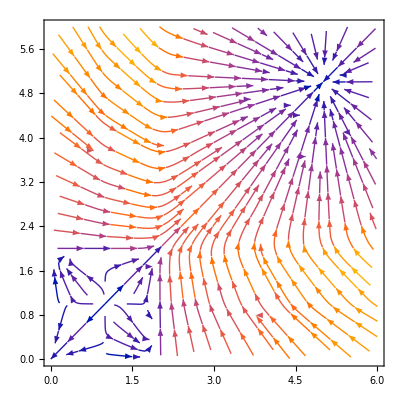

```mathematica
StreamPlot[{eq1,eq2},{x1, 0, 6},{x2, 0, 6}]
```

```mathematica
Solve[eq1==0&&eq2==0, {x1, x2}]
```

```mathematica
J = {{a, b, b, b}, {b, a, b, b}, {b, b, a, b}, {b, b, b, a}}
```

{{a,b,b,b},{b,a,b,b},{b,b,a,b},{b,b,b,a}}

```mathematica
Eigenvectors[J]
```

{{-1,0,0,1},{-1,0,1,0},{-1,1,0,0},{1,1,1,1}}

### GLV competitive with type II functional response

```mathematica
fun[A_, x_, i_, n_] := 1- x[[i]] -Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n = 3;
A = Array[Subscript[a,#1,#2]&,{n,n}]
X = Array[Subscript[x,#1]&,n] 
fun[A, X, 1, n]
```

{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)},{a_(3,1),a_(3,2),a_(3,3)}}

{x_1,x_2,x_3}

1-x_1-(x_2 a_(1,2))/(1+x_2)-(x_3 a_(1,3))/(1+x_3)

```mathematica
n=4;
A = ConstantArray[1.5, {n, n}];(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
Solve[{ fun[A, X, 1, n]==0, fun[A, X, 2, n]==0, fun[A, X, 3, n]==0,  fun[A, X, 4, n]==0}, X]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x_1→-4.71221,x_2→-4.71221,x_3→-4.71221,x_4→-4.71221},{x_1→0.,x_2→0.,x_3→0.5,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.5,x_4→0.},{x_1→0.2,x_2→0.2,x_3→0.2,x_4→0.25},{x_1→0.2,x_2→0.2,x_3→0.25,x_4→0.2},{x_1→0.2,x_2→0.25,x_3→0.2,x_4→0.2},{x_1→0.212214,x_2→0.212214,x_3→0.212214,x_4→0.212214},{x_1→0.25,x_2→0.2,x_3→0.2,x_4→0.2},{x_1→0.5,x_2→0.,x_3→0.,x_4→0.5},{x_1→0.5,x_2→0.,x_3→0.5,x_4→0.},{x_1→0.5,x_2→0.5,x_3→0.,x_4→0.}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x_1→-4.71221,x_2→-4.71221,x_3→-4.71221,x_4→-4.71221},{x_1→0.,x_2→0.,x_3→0.5,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.,x_4→0.5},{x_1→0.,x_2→0.5,x_3→0.5,x_4→0.},{x_1→0.2,x_2→0.2,x_3→0.2,x_4→0.25},{x_1→0.2,x_2→0.2,x_3→0.25,x_4→0.2},{x_1→0.2,x_2→0.25,x_3→0.2,x_4→0.2},{x_1→0.212214,x_2→0.212214,x_3→0.212214,x_4→0.212214},{x_1→0.25,x_2→0.2,x_3→0.2,x_4→0.2},{x_1→0.5,x_2→0.,x_3→0.,x_4→0.5},{x_1→0.5,x_2→0.,x_3→0.5,x_4→0.},{x_1→0.5,x_2→0.5,x_3→0.,x_4→0.}}

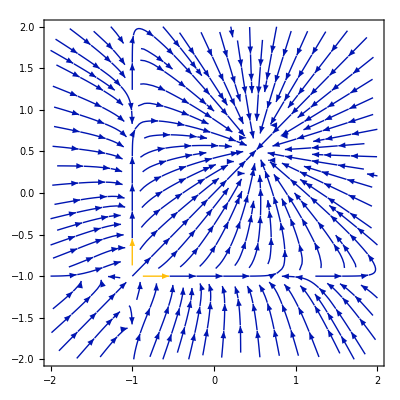

```mathematica
StreamPlot[{fun[A,S, R, X, 1, n],fun[A, S,R, X, 2, n]}, {Subscript[x, 1], -2, 2}, {Subscript[x, 2], -2, 2}]
```

```mathematica
fun[A,S, R, X, 1, n]
```

Part::partd1: Depth of object {0.9,0.9} is not sufficient for the given part specification.

Part::partd: Part specification {0.9,0.9}⟦1,1⟧ is longer than depth of object.

0.5-{0.9,0.9}⟦1,1⟧ x_1-(0.0852691 x_1)/(1+x_1)-(0.145633 x_2)/(1+x_2)

### Symmetric case

```mathematica
eq1 = 1 - x1 - δ*x2/(1+x2) - δ*x3/(1+x3); 
eq2 = 1 - x2 - δ*x1/(1+x1) - δ*x3/(1+x3);
eq3 = 1 - x3 - δ*x1/(1+x1) - δ*x2/(1+x2);
symeq1 = FullSimplify[eq1/.x1->x/.x2->x/.x3->x]
```

1+x (-1-(2 δ)/(1+x))

```mathematica
Solve[symeq1==0,x ]
```

{{x→-δ-√(1+δ^2)},{x→-δ+√(1+δ^2)}}

```mathematica
eq1sym = eq1/.x1->y/.x2->z/.x3->z;
eq2sym =eq3/.x1->y/.x2->z/.x3->z;
FullSimplify[Solve[{eq1sym==0,eq2sym==0}, {y, z}]]
```

{{y→-3+2 δ,z→-(-2+δ)/(2 (-1+δ))},{y→-δ-√(1+δ^2),z→-δ-√(1+δ^2)},{y→-δ+√(1+δ^2),z→-δ+√(1+δ^2)}}

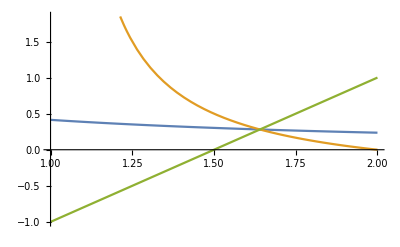

```mathematica
Plot[{-δ+√(1+δ^2),-(-2+δ)/(2 (-1+δ)), -3+2 δ}, {δ, 1, 2}]
```

```mathematica
alpha = D[eq1, x1]/.x1->x/.x2->x/.x3->x
beta = D[eq1, x2]/.x1->x/.x2->x/.x3->x
eig = (alpha - beta)/.x->-δ+√(1+δ^2)
deltac = NSolve[eig==0, δ][[1]][[1]][[2]]
```

1-2 x-(2 x δ)/(1+x)

x ((x δ)/(1+x)^2-δ/(1+x))

1-2 (-δ+√(1+δ^2))-(2 δ (-δ+√(1+δ^2)))/(1-δ+√(1+δ^2))-(-δ+√(1+δ^2)) ((δ (-δ+√(1+δ^2)))/((1-δ+√(1+δ^2))^2)-δ/(1-δ+√(1+δ^2)))

1.64039

```mathematica
neq1 = eq1/.δ->deltac;
neq2 = eq2/.δ->deltac;
neq3 = eq3/.δ->deltac;
Solve[{neq1==0, neq2==0, neq3==0, x1>0, x2>0, x3>0}, {x1, x2, x3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.280776,x2→0.280776,x3→0.280776},{x1→0.280776,x2→0.280776,x3→0.280776},{x1→0.280776,x2→0.280776,x3→0.280776},{x1→0.280776,x2→0.280776,x3→0.280776}}

```mathematica
neq1 = eq1/.δ->deltac+0.1;
neq2 = eq2/.δ->deltac+0.1;
neq3 = eq3/.δ->deltac+0.1;
Solve[{neq1==0, neq2==0, neq3==0, x1>0, x2>0, x3>0}, {x1, x2, x3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.175321,x2→0.175321,x3→0.480776},{x1→0.175321,x2→0.480776,x3→0.175321},{x1→0.266837,x2→0.266837,x3→0.266837},{x1→0.480776,x2→0.175321,x3→0.175321}}

### Sparse interactions (n)

```mathematica
fun[A_, x_, i_, n_] := -1- x[[i]] +Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n=5;
A = {{0, a, a, a,a}, {a, 0, a, a, a}, {a, a, 0, a, a}, {a, a, a, 0, a}, {a, a, a, a, 0}};(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
eq1 = fun[A, X, 1, n];
eq2 = fun[A, X, 2, n];
eq3 = fun[A, X, 3, n];
eq4 = fun[A, X, 4, n];
eq5 = fun[A, X, 5, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/. X[[5]]->x];
sols = Solve[symeq1==0, x]
xsym = sols[[2]][[1]][[2]]
```

{{x→-1+2 a-2 √(-a+a^2)},{x→-1+2 a+2 √(-a+a^2)}}

-1+2 a+2 √(-a+a^2)

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[5]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
```

-1

a/(4 (a+√((-1+a) a))^2)

a/(4 (a+√((-1+a) a))^2)

a/(4 (a+√((-1+a) a))^2)

«1 more identical outputs»

```mathematica
J = {{-1, a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2),a/(4 (a+√((-1+a) a))^2),  a/(4 (a+√((-1+a) a))^2)}, {a/(4 (a+√((-1+a) a))^2), -1, a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2)}, {a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2), -1, a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2)}, {a/(4 (a+√((-1+a) a))^2),a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2), -1, a/(4 (a+√((-1+a) a))^2)},  {a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2), a/(4 (a+√((-1+a) a))^2), -1}};
eig1 = FullSimplify[Eigenvalues[J][[5]]]
acrit = NSolve[eig1==0, a][[1]][[1]][[2]]
```

1/(4 (a+√((-1+a) a))^2)Root[-648 a^5+42120 a^6-381440 a^7+1126400 a^8-1310720 a^9+524288 a^10+7560 a^5 √((-1+a) a)-145920 a^6 √((-1+a) a)+667648 a^7 √((-1+a) a)-1048576 a^8 √((-1+a) a)+524288 a^9 √((-1+a) a)+(945 a^4-37440 a^5+200960 a^6-327680 a^7+163840 a^8-8640 a^4 √((-1+a) a)+98560 a^5 √((-1+a) a)-245760 a^6 √((-1+a) a)+163840 a^7 √((-1+a) a)) #1+(-540 a^3+11280 a^4-30720 a^5+20480 a^6+3600 a^3 √((-1+a) a)-20480 a^4 √((-1+a) a)+20480 a^5 √((-1+a) a)) #1^2+(150 a^2-1280 a^3+1280 a^4-640 a^2 √((-1+a) a)+1280 a^3 √((-1+a) a)) #1^3+(-20 a+40 a^2+40 a √((-1+a) a)) #1^4+#1^5&,5]

1.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

{}⟦2⟧

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
neq5 = eq5/.a-> acrit;
```

```mathematica
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0}, X]
```

{{x_1→-5.44949,x_3→-0.775255,x_2→-5.44949,x_4→-0.775255,x_5→-5.44949},{x_1→-5.44949,x_3→-5.44949,x_2→-0.775255,x_4→-5.44949,x_5→-0.775255},{x_1→-5.44949,x_3→-5.44949,x_2→-0.775255,x_4→-0.775255,x_5→-5.44949},{x_1→-5.44949,x_3→-0.775255,x_2→-0.775255,x_4→-5.44949,x_5→-5.44949},{x_1→-0.775255,x_3→-5.44949,x_2→-5.44949,x_4→-5.44949,x_5→-0.775255},{x_1→-0.775255,x_3→-5.44949,x_2→-5.44949,x_4→-0.775255,x_5→-5.44949},{x_1→-0.775255,x_3→-5.44949,x_2→-0.775255,x_4→-5.44949,x_5→-5.44949},{x_1→-5.44949,x_3→-0.775255,x_2→-5.44949,x_4→-5.44949,x_5→-0.775255},{x_1→-0.775255,x_3→-0.775255,x_2→-5.44949,x_4→-5.44949,x_5→-5.44949},{x_1→-3.22474,x_3→-3.22474,x_2→-0.55051,x_4→-0.55051,x_5→-0.55051},{x_1→-0.55051,x_3→-3.22474,x_2→-0.55051,x_4→-3.22474,x_5→-0.55051},{x_1→-3.22474,x_3→-0.55051,x_2→-0.55051,x_4→-0.55051,x_5→-3.22474},{x_1→-0.55051,x_3→-3.22474,x_2→-3.22474,x_4→-0.55051,x_5→-0.55051},{x_1→-0.55051,x_3→-0.55051,x_2→-3.22474,x_4→-3.22474,x_5→-0.55051},{x_1→-0.55051,x_3→-0.55051,x_2→-3.22474,x_4→-0.55051,x_5→-3.22474},{x_1→-0.55051,x_3→-3.22474,x_2→-0.55051,x_4→-0.55051,x_5→-3.22474},{x_1→-0.55051,x_3→-0.55051,x_2→-0.55051,x_4→-3.22474,x_5→-3.22474},{x_1→-3.22474,x_3→-0.55051,x_2→-3.22474,x_4→-0.55051,x_5→-0.55051},{x_1→-3.22474,x_3→-0.55051,x_2→-0.55051,x_4→-3.22474,x_5→-0.55051},{x_1→-2.33333,x_3→-0.25,x_2→-0.25,x_4→-0.25,x_5→-0.25},{x_1→-0.25,x_3→-0.25,x_2→-0.25,x_4→-0.25,x_5→-2.33333},{x_1→-0.25,x_3→-0.25,x_2→-0.25,x_4→-2.33333,x_5→-0.25},{x_1→-0.25,x_3→-2.33333,x_2→-0.25,x_4→-0.25,x_5→-0.25},{x_1→-0.25,x_3→-0.25,x_2→-2.33333,x_4→-0.25,x_5→-0.25},{x_1→1.-2.25439×10^-9 ⅈ,x_3→1.-2.25439×10^-9 ⅈ,x_2→1.-2.25439×10^-9 ⅈ,x_4→1.-2.25439×10^-9 ⅈ,x_5→1.-2.25439×10^-9 ⅈ},{x_1→1.+1.67956×10^-9 ⅈ,x_3→1.+1.67956×10^-9 ⅈ,x_2→1.+1.67956×10^-9 ⅈ,x_4→1.+1.67956×10^-9 ⅈ,x_5→1.+1.67956×10^-9 ⅈ},{x_1→1.+1.88609×10^-9 ⅈ,x_3→1.+1.88609×10^-9 ⅈ,x_2→1.+1.88609×10^-9 ⅈ,x_4→1.+1.88609×10^-9 ⅈ,x_5→1.+1.88609×10^-9 ⅈ}}

```mathematica
neq1 = eq1/.a->acrit+0.01;
neq2 = eq2/.a->acrit+0.01;
neq3 = eq3/.a->acrit+0.01;
neq4 = eq4/.a->acrit+0.01;
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0, X[[1]]>0, X[[2]]>0, X[[3]]>0, X[[4]]>0, X[[5]]>0 }, X]
```

{{x_1→1.19904,x_3→1.19904,x_2→1.19904,x_4→1.19904,x_5→1.18103},{x_1→0.839346,x_3→0.839346,x_2→0.839346,x_4→0.839346,x_5→0.825314},{x_1→0.839346,x_3→0.839346,x_2→0.839346,x_4→0.839346,x_5→0.825314}}

### Sparse interactions (n-1)

```mathematica
fun[A_, x_, i_, n_] := -1- x[[i]] +Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n=5;
A = {{0, a, a, a,0}, {0, 0, a, a, a}, {a, 0, 0, a, a}, {a, a, 0, 0, a}, {a, a, a, 0, 0}};(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
eq1 = fun[A, X, 1, n];
eq2 = fun[A, X, 2, n];
eq3 = fun[A, X, 3, n];
eq4 = fun[A, X, 4, n];
eq5 = fun[A, X, 5, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/. X[[5]]->x];
sols = Solve[symeq1==0, x]
xsym = sols[[2]][[1]][[2]]
```

{{x→1/2 (-2+3 a-√3 √(-4 a+3 a^2))},{x→1/2 (-2+3 a+√3 √(-4 a+3 a^2))}}

1/2 (-2+3 a+√3 √(-4 a+3 a^2))

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[5]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
```

-1

(4 a)/(3 a+√3 √(a (-4+3 a)))^2

(4 a)/(3 a+√3 √(a (-4+3 a)))^2

(4 a)/(3 a+√3 √(a (-4+3 a)))^2

0

```mathematica
J = {{-1, (4 a)/(3 a+√3 √(a (-4+3 a)))^2, (4 a)/(3 a+√3 √(a (-4+3 a)))^2,(4 a)/(3 a+√3 √(a (-4+3 a)))^2,  0}, {0, -1, (4 a)/(3 a+√3 √(a (-4+3 a)))^2, (4 a)/(3 a+√3 √(a (-4+3 a)))^2, (4 a)/(3 a+√3 √(a (-4+3 a)))^2}, {(4 a)/(3 a+√3 √(a (-4+3 a)))^2, 0, -1, (4 a)/(3 a+√3 √(a (-4+3 a)))^2, (4 a)/(3 a+√3 √(a (-4+3 a)))^2}, {(4 a)/(3 a+√3 √(a (-4+3 a)))^2,(4 a)/(3 a+√3 √(a (-4+3 a)))^2, 0, -1, (4 a)/(3 a+√3 √(a (-4+3 a)))^2},  {(4 a)/(3 a+√3 √(a (-4+3 a)))^2, (4 a)/(3 a+√3 √(a (-4+3 a)))^2, (4 a)/(3 a+√3 √(a (-4+3 a)))^2,0, -1}};
eig1 = FullSimplify[Eigenvalues[J][[5]]]
acrit = NSolve[eig1==0, a][[1]][[1]][[2]]
```

1/(3 a+√3 √(a (-4+3 a)))^2 Root[-190464 a^5+7994880 a^6-52669440 a^7+115706880 a^8-100776960 a^9+30233088 a^10+499200 √3 a^5 √(a (-4+3 a))-6773760 √3 a^6 √(a (-4+3 a))+22892544 √3 a^7 √(a (-4+3 a))-26873856 √3 a^8 √(a (-4+3 a))+10077696 √3 a^9 √(a (-4+3 a))+(83200 a^4-2304000 a^5+9175680 a^6-11197440 a^7+4199040 a^8-180480 √3 a^4 √(a (-4+3 a))+1503360 √3 a^5 √(a (-4+3 a))-2799360 √3 a^6 √(a (-4+3 a))+1399680 √3 a^7 √(a (-4+3 a))) #1+(-15040 a^3+228960 a^4-466560 a^5+233280 a^6+24480 √3 a^3 √(a (-4+3 a))-103680 √3 a^4 √(a (-4+3 a))+77760 √3 a^5 √(a (-4+3 a))) #1^2+(1360 a^2-8640 a^3+6480 a^4-1440 √3 a^2 √(a (-4+3 a))+2160 √3 a^3 √(a (-4+3 a))) #1^3+(-60 a+90 a^2+30 √3 a √(a (-4+3 a))) #1^4+#1^5&,5]

1.33333

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

{}⟦2⟧

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
neq5 = eq5/.a-> acrit;
```

```mathematica
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0}, X]
```

{{x_1→-1.61703,x_3→-0.782959,x_2→-9.08709,x_4→-1.97943,x_5→-0.817481},{x_1→-1.97943,x_3→-1.61703,x_2→-0.817481,x_4→-9.08709,x_5→-0.782959},{x_1→-0.817481,x_3→-9.08709,x_2→-1.61703,x_4→-0.782959,x_5→-1.97943},{x_1→-0.782959,x_3→-0.817481,x_2→-1.97943,x_4→-1.61703,x_5→-9.08709},{x_1→-9.08709,x_3→-1.97943,x_2→-0.782959,x_4→-0.817481,x_5→-1.61703},{x_1→0.446077,x_3→-2.46962,x_2→-0.640327,x_4→-6.42258,x_5→-0.721844},{x_1→-2.46962,x_3→-0.721844,x_2→-6.42258,x_4→0.446077,x_5→-0.640327},{x_1→-0.721844,x_3→-0.640327,x_2→0.446077,x_4→-2.46962,x_5→-6.42258},{x_1→-0.640327,x_3→-6.42258,x_2→-2.46962,x_4→-0.721844,x_5→0.446077},{x_1→-6.42258,x_3→0.446077,x_2→-0.721844,x_4→-0.640327,x_5→-2.46962},{x_1→-3.76019,x_3→-1.8064,x_2→-0.636026,x_4→-0.719319,x_5→1.47322},{x_1→-0.719319,x_3→-3.76019,x_2→1.47322,x_4→-0.636026,x_5→-1.8064},{x_1→-0.636026,x_3→-0.719319,x_2→-1.8064,x_4→1.47322,x_5→-3.76019},{x_1→1.47322,x_3→-0.636026,x_2→-3.76019,x_4→-1.8064,x_5→-0.719319},{x_1→-1.8064,x_3→1.47322,x_2→-0.719319,x_4→-3.76019,x_5→-0.636026},{x_1→-0.560888,x_3→-0.251532,x_2→1.00348,x_4→0.196926,x_5→-2.48335},{x_1→-0.251532,x_3→-2.48335,x_2→0.196926,x_4→-0.560888,x_5→1.00348},{x_1→-2.48335,x_3→1.00348,x_2→-0.560888,x_4→-0.251532,x_5→0.196926},{x_1→1.00348,x_3→0.196926,x_2→-0.251532,x_4→-2.48335,x_5→-0.560888},{x_1→0.196926,x_3→-0.560888,x_2→-2.48335,x_4→1.00348,x_5→-0.251532},{x_1→1.+2.37352×10^-9 ⅈ,x_3→1.+2.37352×10^-9 ⅈ,x_2→1.+2.37352×10^-9 ⅈ,x_4→1.+2.37352×10^-9 ⅈ,x_5→1.+2.37352×10^-9 ⅈ},{x_1→1.-2.65614×10^-9 ⅈ,x_3→1.-2.65614×10^-9 ⅈ,x_2→1.-2.65614×10^-9 ⅈ,x_4→1.-2.65614×10^-9 ⅈ,x_5→1.-2.65614×10^-9 ⅈ}}

```mathematica
neq1 = eq1/.a->acrit+0.01;
neq2 = eq2/.a->acrit+0.01;
neq3 = eq3/.a->acrit+0.01;
neq4 = eq4/.a->acrit+0.01;
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0, X[[1]]>0, X[[2]]>0, X[[3]]>0, X[[4]]>0, X[[5]]>0 }, X]
```

{{x_1→1.17214,x_3→1.16947,x_2→1.16871,x_4→1.1693,x_5→1.15677},{x_1→0.861069,x_3→0.858486,x_2→0.857483,x_4→0.858205,x_5→0.848319}}

### Sparse interactions (n-2)

```mathematica
fun[A_, x_, i_, n_] := -1- x[[i]] +Sum[A[[i,j]]*x[[j]]/(1+x[[j]]), {j, DeleteCases[Range[1,n],i]}];
```

```mathematica
n=5;
A = {{0, a, a, 0,0}, {0, 0, a, a, 0}, {0, 0, 0, a, a}, {a, 0, 0, 0, a}, {a, a, 0, 0, 0}};(*ResourceFunction["RandomMatrix"][Real,{0,0.1},{n,n}];*)
X =Array[Subscript[x,#1]&,n] ;  
eq1 = fun[A, X, 1, n];
eq2 = fun[A, X, 2, n];
eq3 = fun[A, X, 3, n];
eq4 = fun[A, X, 4, n];
eq5 = fun[A, X, 5, n];
symeq1 = FullSimplify[eq1/.X[[1]]->x/.X[[2]]->x/.X[[3]]->x/.X[[4]]->x/. X[[5]]->x];
sols = Solve[symeq1==0, x]
xsym = sols[[2]][[1]][[2]]
```

{{x→-1+a-√(-2 a+a^2)},{x→-1+a+√(-2 a+a^2)}}

-1+a+√(-2 a+a^2)

```mathematica
J11 =FullSimplify[ D[eq1, X[[1]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J12 = FullSimplify[D[eq1,X[[2]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J13 =FullSimplify [D[eq1, X[[3]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[4]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
J14 =FullSimplify [D[eq1, X[[5]]]/.X[[1]]->xsym/.X[[2]]->xsym/.X[[3]]->xsym/.X[[4]]->xsym/.X[[5]]->xsym]
```

-1

a/(a+√((-2+a) a))^2

a/(a+√((-2+a) a))^2

0

0

```mathematica
J = {{-1, a/(a+√((-2+a) a))^2, a/(a+√((-2+a) a))^2,0,  0}, {0, -1, a/(a+√((-2+a) a))^2, a/(a+√((-2+a) a))^2, 0}, {0, 0, -1, a/(a+√((-2+a) a))^2, a/(a+√((-2+a) a))^2}, {a/(a+√((-2+a) a))^2,0, 0, -1, a/(a+√((-2+a) a))^2},  {a/(a+√((-2+a) a))^2, a/(a+√((-2+a) a))^2, 0,0, -1}};
eig1 = FullSimplify[Eigenvalues[J][[1]]]
acrit = NSolve[eig1==0, a][[1]][[1]][[2]]
```

1/(a+√((-2+a) a))^2 Root[-44 a^5+870 a^6-3240 a^7+4480 a^8-2560 a^9+512 a^10+190 a^5 √((-2+a) a)-1320 a^6 √((-2+a) a)+2688 a^7 √((-2+a) a)-2048 a^8 √((-2+a) a)+512 a^9 √((-2+a) a)+(95 a^4-1300 a^5+3200 a^6-2560 a^7+640 a^8-340 a^4 √((-2+a) a)+1600 a^5 √((-2+a) a)-1920 a^6 √((-2+a) a)+640 a^7 √((-2+a) a)) #1+(-85 a^3+720 a^4-960 a^5+320 a^6+240 a^3 √((-2+a) a)-640 a^4 √((-2+a) a)+320 a^5 √((-2+a) a)) #1^2+(40 a^2-160 a^3+80 a^4-80 a^2 √((-2+a) a)+80 a^3 √((-2+a) a)) #1^3+(-10 a+10 a^2+10 a √((-2+a) a)) #1^4+#1^5&,1]

2.

```mathematica
neq1 = eq1/.a->acrit;
neq2 = eq2/.a->acrit;
neq3 = eq3/.a->acrit;
neq4 = eq4/.a->acrit;
neq5 = eq5/.a-> acrit;
```

```mathematica
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0}, X]
```

{{x_1→-0.633877,x_2→-6.34626,x_3→-0.500994,x_4→-0.625348,x_5→-2.08855},{x_1→-0.500994,x_2→-0.625348,x_3→-2.08855,x_4→-0.633877,x_5→-6.34626},{x_1→-6.34626,x_2→-0.500994,x_3→-0.625348,x_4→-2.08855,x_5→-0.633877},{x_1→-2.08855,x_2→-0.633877,x_3→-6.34626,x_4→-0.500994,x_5→-0.625348},{x_1→-0.625348,x_2→-2.08855,x_3→-0.633877,x_4→-6.34626,x_5→-0.500994},{x_1→-0.16718,x_2→-3.58866,x_3→-0.492358,x_4→-0.244962,x_5→1.37112},{x_1→-0.492358,x_2→-0.244962,x_3→1.37112,x_4→-0.16718,x_5→-3.58866},{x_1→1.37112,x_2→-0.16718,x_3→-3.58866,x_4→-0.492358,x_5→-0.244962},{x_1→-3.58866,x_2→-0.492358,x_3→-0.244962,x_4→1.37112,x_5→-0.16718},{x_1→-0.244962,x_2→1.37112,x_3→-0.16718,x_4→-3.58866,x_5→-0.492358},{x_1→1.-5.70815×10^-8 ⅈ,x_2→1.-5.70815×10^-8 ⅈ,x_3→1.-5.70815×10^-8 ⅈ,x_4→1.-5.70815×10^-8 ⅈ,x_5→1.-5.70815×10^-8 ⅈ},{x_1→1.+6.25775×10^-8 ⅈ,x_2→1.+6.25775×10^-8 ⅈ,x_3→1.+6.25775×10^-8 ⅈ,x_4→1.+6.25775×10^-8 ⅈ,x_5→1.+6.25775×10^-8 ⅈ}}

```mathematica
neq1 = eq1/.a->acrit+0.01;
neq2 = eq2/.a->acrit+0.01;
neq3 = eq3/.a->acrit+0.01;
neq4 = eq4/.a->acrit+0.01;
NSolve[{neq1==0,neq2==0,neq3==0,neq4==0, neq5==0, X[[1]]>0, X[[2]]>0, X[[3]]>0, X[[4]]>0, X[[5]]>0 }, X]
```

{{x_1→1.13778,x_2→1.13708,x_3→1.13448,x_4→1.13549,x_5→1.1286},{x_1→0.884021,x_2→0.883279,x_3→0.880806,x_4→0.881969,x_5→0.876463}}